## PHAS0012 Computing for Mathematical Physics 2019/20

# Homework 7

# Mark for homework 7: /72 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Which feedback from your last homework are you employing in this homework? Marks will be deducted if you do not complete this section. Implemented text and subsections; now also used code cells format to make clearer, and have broken up code cells for better readability- this is from week 1 and 3 feedback, had no feedback on week 2. From week 5 I have ensured to label all graphs

# Give your answers in the code cells labelled “(*your solution here*)”

## Question 1:

1. We may simulate a sequence of dice rolls by choosing a random integer between 1 and 6 (inclusive). Write a function that will generate the results of n tosses, and return a list which describes how the cumulative total varies through the generated random sequence. Use FoldList to do this.

```mathematica
f1a[n_]:=FoldList[Plus,RandomInteger[{1,6 },n]]
f1a[6]
```

{4,9,10,11,14,15}

The expected cumulative total would be 3.5 times the number of tosses. Using your function, plot the difference between the calculated cumulative total and the expected cumulative total. Do this for 25000 tosses. [8 marks]

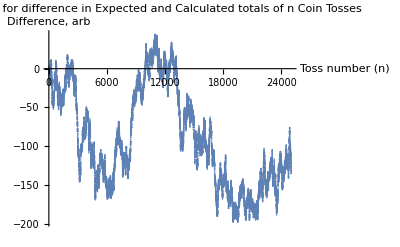

```mathematica
f1b[n_]:= Module[{cumlist, explist, diff},
{cumlist=FoldList[Plus,RandomInteger[{1,6 },n]], explist=Table[3.5 i,{i,1n}], diff= cumlist-explist};
ListPlot[diff, AxesLabel->{"Toss number (n)", "Difference, arb"}, 
PlotLabel->"Plot for difference in Expected 
and Calculated totals of n Coin Tosses"]]
f1b[25000]
```

## Question 2:

2. The expression

F(x) = (1+x)Exp[x]

can be expressed as an infinite series by

F(x) = ∑_(k=0)^∞ (k+1)/(k!)x^k

In this question, you will use a variety of different techniques in Mathematica to write a function that will be used to calculate an approximation of F(0.32) using this series expansion. In each case, there is a parameter or part of an expression within your code that will limit the accuracy of the result. Identify this separately in all parts of the question within a text cell. You might have to use other functions as well to sum up all elements of a list.

#### True value at precision 20 digits:

```mathematica
f2a[x_]=(1+x)E^x
true=SetPrecision[f2a[0.32],20]
```

ⅇ^x (1+x)

1.8178086489234634993

#### Part a:

a) Construct a rule to set x=0.32 to a precision of 20 digits. [2 marks]

```mathematica
rul2=x:>SetPrecision[0.32,20]
```

x:>SetPrecision[0.32,20]

#### Part b:

b) Use Table to evaluate the expansion for F(0.32), use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy. [6 marks]

```mathematica
f2b[n_]:=Total[Table[((k+1)/(k!)x^k), {k,0, n}]]
```

Created a function which takes a number of iterations as a inputs, and uses Table to outputs the F(x) summation iterated to the value given.

```mathematica
f2b[10]
{f2b[15], f2b[16], f2b[17]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the function by the element of the Table which sets max value for k. Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

#### Part c:

c) Use a For loop to evaluate the expansion for F(0.32), use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy. [5 marks]

```mathematica
f2c[n_]:= Module[{sum}, sum=0;
For[k=0,k≤n, k++, sum+=(k+1)/(k!)x^k];
sum]
```

Created a function which takes a number of iterations as a inputs, and uses a For loop to sum over iterations of the F (x) summation, each pass sums the summation at that value of k and adds one to k, repeating until n is reached- outputting the resulting sum.

```mathematica
f2c[10]
{f2c[15], f2c[16], f2c[17]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the For function by the ‘test’ element which allows the loop to run until evaluated False, as the test is for k<=n this iterates for n values.  Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

#### Part d:

d) Use a Do loop to evaluate the expansion for F(0.32), use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy. [5 marks]

```mathematica
f2d[n_]:= Module[{sum}, sum=0;
Do[sum+=(k+1)/(k!)x^k, {k,0,n}];
sum]
```

Created a function which takes a number of iterations as a inputs, and uses a Do loop to sum over iterations of the F (x) summation, each pass sums the summation at that value of k, after n times it completes and outputs the resulting sum.

```mathematica
f2d[10]
{f2d[15], f2d[16], f2d[17]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the function by the element of the Do function which sets no. of iterations/ max value for k to be evaluated.  Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

#### Part e:

e) Use a While loop to evaluate the expansion for F(0.32), use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy.  [5 marks]

```mathematica
f2e[n_]:= Module[{sum, k}, {sum=0, k=0};
While[k≤ n, sum+=(k+1)/(k!)x^k; k=k+1];
sum]
```

Created a function which takes a number of iterations as a inputs, and uses a While loop to sum over iterations of the F (x) summation, each pass sums the summation at that value of k, and adds one to k; repeating while k is less then n when completed it outputs the resulting sum.

```mathematica
f2e[10]
{f2e[15], f2e[16], f2e[17]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the While function by the ‘test’ element which allows the loop to run while the test is True, as the test is for k<=n this iterates for n values.  Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

#### Part f:

f) Use a While loop with a fundamentally different loop termination condition to that used in part (e) to evaluate the expansion for F(0.32),use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy. [5 marks]

```mathematica
f2f[precision_]:= Module[{test, sum, k}, {test= False;sum=0; k=0}; 
While[!test, sum+=(k+1)/(k!)x^k; k=k+1; test=Evaluate[k/((k-1)!)x^(k-1)/.rul2]≤precision];
sum]
```

Created a function which takes a number of iterations as a inputs, and uses a While loop to sum over iterations of the F (x) summation, each pass sums the summation at that value of k and adds one to the value of k, it repeating while the next value is greater then given precision, when completed it outputs the resulting sum.

```mathematica
f2f[10^-19]
{f2f[10^-18], f2f[10^-19], f2f[10^-20]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800+x^11/3326400+(13 x^12)/479001600+x^13/444787200+x^14/5811886080+x^15/81729648000+(17 x^16)/20922789888000

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by precision defined in the function, which controls the number of iterations, this is controlled in the While function by the ‘test’ element which allows the loop to run while the test is True. Here the test Evaluates the last value added to the summation (using the earlier rule) and if lower than a certain precision returns False. This iterates for up to the specified precision. Therefore, the accuracy is more so limited by precision of x when using the rule; we can see for the output after precision of 10^-20 the evaluation of the sum is constant up to a precision of 19 (as expected due to the rule substituting up to a precision off 20).

#### Part g:

g)  Use Fold or FoldList to evaluate the expansion for F(0.32),use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy.  [8 marks]

```mathematica
f2g[n_]:=Fold[#1+(#2+1)/(#2!)x^#2&,1,Table[i,{i,1,n}]]
```

Created a function which takes a number of iterations as a inputs, and uses Fold to sum over iterations of the F (x) summation; the function produces a list of integers from 1 to n, then folds the list, using a Pure Function  that adds to the first element (the sum), by taking the second (k) and passing it through the function being summed; outputting the sum to n values.

```mathematica
f2g[10]
{f2g[15], f2g[16], f2g[17]}/.rul2
```

1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800

{1.8178086489234633728,1.8178086489234633729,1.8178086489234633729}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the Table function by the max value that the list from 1-n goes, thus determining the amount the list is folded/ it iterates for n values.  Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

#### Part h:

h) Use Nest or NestList to evaluate the expansion for F(0.32), use a text cell to identify the parameter in your expression which limits the accuracy of the obtained answer and explain how it limits the accuracy.  [8 marks]

```mathematica
f2h[n_]:=  Rest[Nest[ {#[[1]]+1,#[[2]]+(#[[1]]+1)/(#[[1]]!)x^(#[[1]])}&, {1,1}, n] ]
```

Created a function which takes a number of iterations as a inputs, and uses Nest to sum over iterations of the F (x) summation; takes the list {1,1}, which is Nested with the Pure Function n times; the Pure Function, first takes the first element of the list and adds one ( effectively counting the value k), next it takes the second element and adds to it the function evaluated at the value of k denoted in the first element of the list.

```mathematica
f2h[10]
{f2h[15], f2h[16], f2h[17]}/.rul2
```

{1+2 x+(3 x^2)/2+(2 x^3)/3+(5 x^4)/24+x^5/20+(7 x^6)/720+x^7/630+x^8/4480+x^9/36288+(11 x^10)/3628800}

{{1.8178086489234633728},{1.8178086489234633729},{1.8178086489234633729}}

Accuracy of the evaluation is limited here by n, the number of iterations, this is controlled in the Nest function by the number of times it repeats, thus it iterates for n values.  Accuracy is also limited by precision of x when using the rule; we can see in the out put after 16 iterations the evaluation is constant up to a precision of 20.

## Question 3:

3. The Koch snowflake is a well-known fractal object, well suited to an iterative construction. One starts with a triangle and repeatedly draws smaller triangles on the outside of each side.

#### Part a:

a) Define a list of three Lines,  from (0, 0) to (1/2, √3/2), from (1/2, √3/2) to (1, 0), and from (1, 0) to (0, 0). Use Graphics to show the result. [5 marks]

{{{0,0},{1/2,(√3)/2}},{{1/2,(√3)/2},{1,0}},{{1,0},{0,0}}}

{Line[{{0,0},{1/2,(√3)/2}}],Line[{{1/2,(√3)/2},{1,0}}],Line[{{1,0},{0,0}}]}

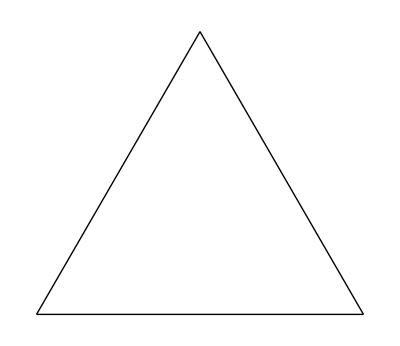

```mathematica
l= {{{0,0},{1/2,(√3)/2}},{{1/2,(√3)/2},{1,0}},{{1,0},{0,0}}}
line= Map[Line,l]
Graphics[line]
```

#### Part b:

b) Write a function, as a Module, which will accept one argument of the form Line[{start,finish}] (each of start and finish is a 2-vector). The function should

i) Calculate the vector vec={x,y}=finish - start;

```mathematica
f3a[Line[{s_List,f_List}]]:= Module[{vec}, vec=f-s; vec]
Map[f3a,line]
```

{{1/2,(√3)/2},{1/2,-(√3)/2},{-1,0}}

ii) Calculate the scaled normal to the line 
            			normal = {-y,x} √3/6;

```mathematica
f3b[Line[{s_List,f_List}]]:= Module[{vec},vec=f-s; {-vec[[2]],vec[[1]]} ((√3)/6)]
Map[f3b,line]
```

{{-1/4,1/(4 √3)},{1/4,1/(4 √3)},{0,-1/(2 √3)}}

iii) Return the list containing four Lines representing one third of the original line, the triangular blip, and the remaining third, that is lines from start to start + vec/3, from start + vec/3 to start + vec/2 + normal, from start + vec/2 + normal to start + 2 vec/3, and from start + 2 vec/3 to finish. [6 marks for function]

```mathematica
f3c[Line[{s_List,f_List}]]:= Module[{vec, normal},{vec=f-s, normal={-vec[[2]],vec[[1]]} ((√3)/6)};
{ Line[{s, s+vec/3}], Line[{s+vec/3, s+vec/2+normal}], Line[{s+vec/2+normal, s+2vec/3}], Line[{s+2vec/3, f}] }]
```

#### Part c:

c) Check your function by applying it to the line from (0,0) to (1,0) and displaying the result. [2 marks]

{Line[{{1,0},{2/3,0}}],Line[{{2/3,0},{1/2,-1/(2 √3)}}],Line[{{1/2,-1/(2 √3)},{1/3,0}}],Line[{{1/3,0},{0,0}}]}

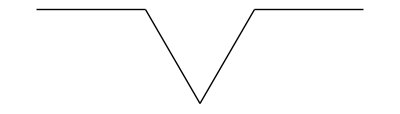

```mathematica
fracline= f3c[line[[3]]]
Graphics[fracline]
```

#### Part d:

d) Next Map your function onto the triangle you created in step (a) and display the result.  [2 marks]

{Line[{{0,0},{1/6,1/(2 √3)}}],Line[{{1/6,1/(2 √3)},{0,1/(4 √3)+(√3)/4}}],Line[{{0,1/(4 √3)+(√3)/4},{1/3,1/(√3)}}],Line[{{1/3,1/(√3)},{1/2,(√3)/2}}],Line[{{1/2,(√3)/2},{2/3,-1/(2 √3)+(√3)/2}}],Line[{{2/3,-1/(2 √3)+(√3)/2},{1,1/(4 √3)+(√3)/4}}],Line[{{1,1/(4 √3)+(√3)/4},{5/6,-1/(√3)+(√3)/2}}],Line[{{5/6,-1/(√3)+(√3)/2},{1,0}}],Line[{{1,0},{2/3,0}}],Line[{{2/3,0},{1/2,-1/(2 √3)}}],Line[{{1/2,-1/(2 √3)},{1/3,0}}],Line[{{1/3,0},{0,0}}]}

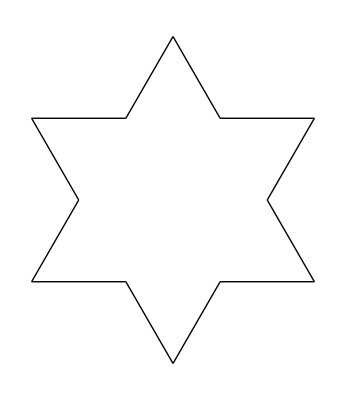

```mathematica
fraclines= Flatten[Map[f3c,line]]
Graphics[fraclines]
```

#### Part e:

e) We can now draw the snowflake. Write a new function Koch to draw the nth Koch snowflake: use Nest and your function to draw the blips iteratively starting from the triangle. Note that as each application of your function introduces an extra list level you will need to Flatten by one level each time you use it. Demonstrate the use of your function by drawing the 4th Koch snowflake. [5 marks]

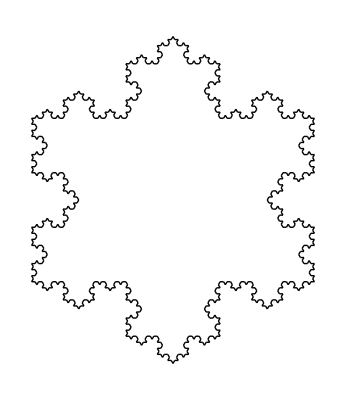

```mathematica
Koch[oritri_, n_]:= Graphics[Nest[Flatten[Map[f3c, #]]&, oritri, n]]
snow= Koch[line,4]
```

Total marks available: 72

Total Marks: 72

Solutions are due by 4pm on Monday March 9th. Make a copy of your solutions with the output deleted (Cell|Delete All Output) and upload it through Moodle.  Please name your file according to the pattern hw7_Bhamrah_Jasvir. Of course, the first thing I shall do when I get the file is to click Evaluation|Evaluate Notebook, so make sure the file you send me will survive that.

A.H. Harker, J. Underwood, L.K. McKemmish, J. Bhamrah
UCL
February 2016, February 2017, February 2020